```mathematica
<<AlexTools`ALXTools`
```

```mathematica
expConfig = Import["N:\\Storage Files\\UCL Data\\Anopheles\\Mosquito 1\\exp_Config.txt","TSV"]; (* imports the generic experiment settings *)

dir = SetDirectory["N:\\Storage Files\\UCL Data\\Culex\\"];
fnames = FileNames["*0_FFT*",dir,Infinity];
typeOfSet = 1;
dataset = {"set_1","ratio"};

frequencyList=If[dataset[[typeOfSet]]=="ratio",ToString/@(Round@Flatten[Import["N:\\Storage Files\\UCL Data\\Aedes\\Mosquito 1\\ratio scan_frequencyList.txt","CSV"]]),expConfig[[7;;,2]]]; 
t= GatherBy[Select[fnames,StringContainsQ[#,dataset[[typeOfSet]]]&],StringSplit[#,"\\"][[5]]&];
t= SortBy[t,ToExpression[StringTake[StringSplit[#[[1]],"\\"][[5]],-2;;]]&]; (* This contains the directories for the amp and frequency profile of EACH mosquito *)

(* healthyFiles contain the directory where each mosquito holds its healthy laser PRESTIM files *)
healthyFiles = SortBy[Select[FileNames["*\\healthy_files*",dir,Infinity],StringContainsQ[#,dataset[[typeOfSet]]~~__~~"Laser_PreStim"]&],ToExpression[StringTake[StringSplit[#,"\\"][[5]],-2;;]]&];
healthyFiles//TableForm
frequencyList
```

N:\Storage Files\UCL Data\Culex\Mosquito 1\set_1\Laser_PreStim\healthy_files
N:\Storage Files\UCL Data\Culex\Mosquito 2\set_1\Laser_PreStim\healthy_files
N:\Storage Files\UCL Data\Culex\Mosquito 3\set_1\Laser_PreStim\healthy_files
N:\Storage Files\UCL Data\Culex\Mosquito 4\set_1\Laser_PreStim\healthy_files
N:\Storage Files\UCL Data\Culex\Mosquito 5\set_1\Laser_PreStim\healthy_files
N:\Storage Files\UCL Data\Culex\Mosquito 6\set_1\Laser_PreStim\healthy_files

{100,100,110,110,120,120,130,130,140,140,150,150,160,160,170,170,180,180,190,190,200,200,210,210,220,220,230,230,240,240,250,250,260,260,270,270,280,280,290,290,300,300,305,305,310,310,315,315,320,320,325,325,330,330,335,335,340,340,345,345,350,350,355,355,360,360,365,365,370,370,375,375,380,380,385,385,390,390,395,395,400,400,410,410,420,420,430,430,440,440,450,450,460,460,470,470,480,480,490,490,500,500,510,510,520,520,530,530,540,540,550,550,560,560,570,570,580,580,590,590,600,600,610,610,620,620,630,630,640,640,650,650,660,660,670,670,680,680,690,690,700,700,710,710,720,720,730,730,740,740,750,750,760,760,770,770,780,780,790,790,800,800,810,810,820,820,830,830,840,840,850,850,860,860,870,870,880,880,890,890,900,900,910,910,920,920,930,930,940,940,950,950,960,960,970,970,980,980,990,990,1000,1000}

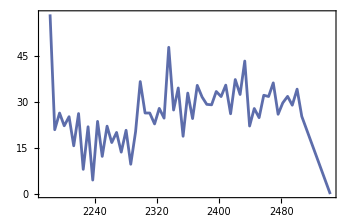

```mathematica
{amp,freq}=readMyFile[#]&/@t[[2]];
amp//ListLinePlot
```

```mathematica
Clear[extractState]

speciesDictionary = <|
"AGA"-><|"minSSOAmp"->135,"ssoRange"->{300,500}|>,
"AAE"-><|"minSSOAmp"->20,"ssoRange"->{300,500}|>,
"CQU"-><|"minSSOAmp"->80,"ssoRange"->{200,400}|>|>;

extractState[file_]:=Block[{healthyExperiments,healthyFilesForThisMosquito,availableFreqs,mosquitoNumber,amp,freq,
experimentalStates,mosIDs,mosquitoSpecies,ssoCondition,ssoRange,ssoState},


mosquitoSpecies = StringSplit[FileNameTake[FileNames["README*",FileNameJoin[StringSplit[file,"\\"][[;;5]]]<>"\\"][[1]]],"_"][[3]] (* extracts the species, AGA, AAE, CQU, etc..*);
mosquitoNumber = ToExpression[StringTake[StringSplit[file,"\\"][[5]],-2;;]] (* extracts the mosquito we are working with*);
{amp, freq}=readMyFile[#,2]&/@t[[mosquitoNumber]];
mosIDs = ("Mos_"<>StringPadLeft[ToString[mosquitoNumber],2,"0"])&/@Range[Length@amp](* extracts the number of the mosquito *);

healthyExperiments=FileNameTake/@FileNames["*.txt",file<>"\\",1] (* extracts the experiments that are healthy*);
healthyFilesForThisMosquito = ToExpression[StringTake[#,If[typeOfSet==2,-7,-8];;-6]]&/@healthyExperiments (* extracts the number associated with this experiment *);
availableFreqs =frequencyList[[healthyFilesForThisMosquito]] (* creates a list of available frequencies*);
experimentalStates = If[OddQ[#],"1T","2T"]&/@healthyFilesForThisMosquito; (* checks if the experiment is a 1T or 2T*)

ssoCondition=speciesDictionary[mosquitoSpecies]["minSSOAmp"];       (* 135nm deflection needed by AGA to achieve 50% neuronal activity - Su et al 2018*)
ssoRange=speciesDictionary[mosquitoSpecies]["ssoRange"]; (* expected values of SSO frequency*)
ssoState = MapThread[If[Between[#1,ssoRange] && #2>=ssoCondition,"SSO",If[Between[#1,ssoRange],"wSSO","QUIES"]]&,{freq,amp}];



{{"Mos_ID","exp_Number","tone","stim_freq_[Hz]","sso_amp_[nm]","sso_freq_[Hz]","sso_state"}}~Join~({mosIDs,healthyFilesForThisMosquito,experimentalStates,availableFreqs,amp,freq,ssoState}ᵀ)
(*Length/@{mosIDs,healthyFilesForThisMosquito,experimentalStates,availableFreqs,amp,freq,ssoState};
healthyExperiments//Length*)


]

extractState[healthyFiles[[4]]];
```

```mathematica
fileData = <|Table["mos_"<>ToString[i]->extractState[healthyFiles[[i]]],{i,Length@healthyFiles}]|>;
```

```mathematica
Directory[]
Export["mechanical_state_"<>StringSplit[dir,"\\"][[-1]]<>If[typeOfSet==1,"","_ratios"]<>".txt",ExportString[fileData,"RawJSON","Compact"-> False]]
```

N:\Storage Files\UCL Data\Culex

mechanical_state_Culex.txt

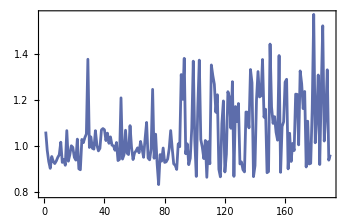

```mathematica
test=Import["mechanical_state_"<>StringSplit[dir,"\\"][[-1]]<>If[typeOfSet==1,"","_ratios"]<>".txt","RawJSON"];
test["mos_4"][[2;;,5]]//ListLinePlot
```

```mathematica
test["mos_5"][[2;;,-1]]//Tally
```

{{wSSO,110},{QUIES,10}}